```mathematica
nf1[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng1[y_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
nf2[y_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng2[y_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
nf3=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
ng3=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->L1,t->-1}];
nf12[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
ng12[y_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
nf22[y_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
ng22[y_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
nf32=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
ng32=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->L1,t->-1}];
```

```mathematica
NIntegrate[I*nf1[y],{y,-0.2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[I*nf2[y],{y,0,0.9},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

3.614491865

```mathematica
NIntegrate[nf12[y],{y,-0.4,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22[y],{y,0,0.8},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-4.121612607 ⅈ

```mathematica
Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,Λ->L1}]
```

((0.+6.28319 ⅈ) k3 (-1.+x)^3 ((3.31174+0. ⅈ) ξ^2-(3.31174+0. ⅈ) ξ^4+t ((1.+0. ⅈ)-(2.+0. ⅈ) ξ^2+(1.+0. ⅈ) ξ^4)))/((1.01944+1.01944 k3^2-1. x)^4 (-1.+ξ^2) (t+3.52688 ξ^2-1. t ξ^2))

```mathematica
NIntegrate[nf32,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

0.+2.6351 ⅈ

```mathematica
NIntegrate[nf3,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

0.+2.6351 ⅈ

```mathematica
NIntegrate[nf12[y],{y,-0.2,0.6},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-2.720290853 ⅈ

```mathematica
NIntegrate[nf1[y],{y,-0.1,0.8},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.937435953 ⅈ

```mathematica
NIntegrate[ng12[y],{y,-0.4,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng22[y],{y,0,0.8},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.38379983 ⅈ

```mathematica
NIntegrate[ng1[y],{y,-0.2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng2[y],{y,0,0.9},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.8909291 ⅈ

```mathematica
NIntegrate[ng32,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
NIntegrate[ng3,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
f32=f3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
g32=g3/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
ft3=f32/.{Q^2->(-t),Q^4->t^2};
gt3=g32/.{Q^2->(-t),Q^4->t^2};
```

```mathematica
nf3=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->1,t->-1}];
ng3=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.1,Λ->1,t->-1}];
```

```mathematica
nf32=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->1,t->-1}];
ng32=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.2,Λ->1,t->-1}];
```

```mathematica
NIntegrate[nf32,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

0.+5.2702 ⅈ

```mathematica
NIntegrate[nf3,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

0.+5.2702 ⅈ

```mathematica
NIntegrate[ng32,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
NIntegrate[ng3,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.+0. ⅈ

```mathematica
ng32
```

0.+0. ⅈ

```mathematica
inf1[y_]:=NIntegrate[nf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
inf2[y_]:=NIntegrate[nf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1[y_]:=NIntegrate[ng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing2[y_]:=NIntegrate[ng2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lf1=ParallelTable[{y,inf1[y]},{y,-0.2,0,0.02}];
lf2=ParallelTable[{y,inf2[y]},{y,0,0.9,0.02}];
lg1=ParallelTable[{y,ing1[y]},{y,-0.2,0,0.02}];
lg2=ParallelTable[{y,ing2[y]},{y,0,0.9,0.02}];
```

```mathematica
sf1=Interpolation[lf1];
sf2=Interpolation[lf2];
sg1=Interpolation[lg1];
sg2=Interpolation[lg2];
```

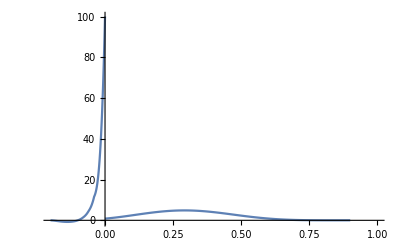

```mathematica
Show[Plot[(I)*sf1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(I)*sf2[x],{x,0,0.9},PlotRange->{{-0.1,1},All}]]
```

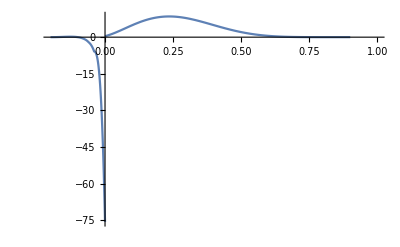

```mathematica
Show[Plot[(I)*sg1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(I)*sg2[x],{x,0,0.9},PlotRange->{{-0.1,1},All}]]
```

```mathematica
path1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-xi1.pdf"}];
```

```mathematica
Export[path1,Labeled[Show[Plot[(I)*sf1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(I)*sf2[x],{x,0,0.9},PlotRange->{{-0.2,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-xi1.pdf

```mathematica
Labeled[Show[Plot[(I)*sf1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(I)*sf2[x],{x,0,0.9},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]]},{Left,Bottom},LabelStyle->24]
```

-Graphics-f_fy

```mathematica
path2=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-xi1.pdf"}];
```

```mathematica
Export[path2,Labeled[Show[Plot[(I)*sg1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(I)*sg2[x],{x,0,0.9},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]]},{Left,Bottom},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-xi1.pdf

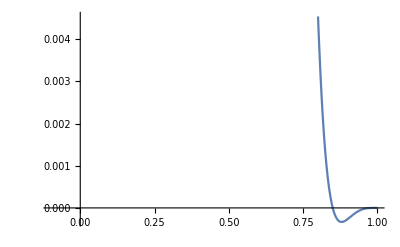
-Graphics-f_2y

```mathematica
Labeled[Show[Plot[(-I)*sf2[x],{x,0.8,1},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,2],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]]},{Left,Bottom},LabelStyle->24]
```

```mathematica
path1g=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-xi1.pdf"}];
```

```mathematica
Export[path1g,Labeled[Show[Plot[(-I)*sg1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All}],Plot[(-I)*sg2[x],{x,0,0.9},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-xi1.pdf

```mathematica
path2g=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"b-g2.pdf"}];
```

```mathematica
Export[path2g,Labeled[Show[Plot[(-I)*sg2[x],{x,0.8,1},PlotRange->{{-0.1,1},All}],AxesStyle->Directive[Thick,16]],
{StyleBox[SubscriptBox[g,2],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]]},{Left,Bottom},LabelStyle->24]]
```

G:\output\summary\gpd\pic\b-g2.pdf

```mathematica
nf1x1[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
ng1x1[y_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
nf2x1[y_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
ng2x1[y_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
nf3x1=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
ng3x1=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.01,Λ->L1,t->-1}];
nf1x2[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
ng1x2[y_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
nf2x2[y_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
ng2x2[y_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
nf3x2=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];
ng3x2=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.001,Λ->L1,t->-1}];nf1x3[y_]=Simplify[ft1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
ng1x3[y_]=Simplify[gt1/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
nf2x3[y_]=Simplify[ft2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
ng2x3[y_]=Simplify[gt2/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
nf3x3=Simplify[ft3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
ng3x3=Simplify[gt3/.{MB->0.939,mm->0.1381,MM->0.939,ξ->0.0001,Λ->L1,t->-1}];
```

```mathematica
inf1[y_]:=NIntegrate[nf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
inf2[y_]:=NIntegrate[nf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing1[y_]:=NIntegrate[ng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing2[y_]:=NIntegrate[ng2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];inf1x1[y_]:=NIntegrate[nf1x1[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
inf2x1[y_]:=NIntegrate[nf2x1[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing1x1[y_]:=NIntegrate[ng1x1[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing2x1[y_]:=NIntegrate[ng2x1[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];inf1x2[y_]:=NIntegrate[nf1x2[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
inf2x2[y_]:=NIntegrate[nf2x2[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing1x2[y_]:=NIntegrate[ng1x2[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing2x2[y_]:=NIntegrate[ng2x2[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];inf1x3[y_]:=NIntegrate[nf1x3[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
inf2x3[y_]:=NIntegrate[nf2x3[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing1x3[y_]:=NIntegrate[ng1x3[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
ing2x3[y_]:=NIntegrate[ng2x3[y],{k3,0,∞},{θ,0,2π},MinRecursion->10,MaxRecursion->50,WorkingPrecision->10,AccuracyGoal->10,Method->{"GlobalAdaptive",Method->"ClenshawCurtisRule"}];
```

```mathematica
lf1=ParallelTable[{y,inf1[y]},{y,-0.2,0,0.02}];
lf2=ParallelTable[{y,inf2[y]},{y,0,0.9,0.02}];
lg1=ParallelTable[{y,ing1[y]},{y,-0.2,0,0.02}];
lg2=ParallelTable[{y,ing2[y]},{y,0,0.9,0.02}];
```

```mathematica
lf1x1=ParallelTable[{y,inf1x1[y]},{y,-0.02,0,0.002}];
lf2x1=ParallelTable[{y,inf2x1[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01]]}];
lg1x1=ParallelTable[{y,ing1x1[y]},{y,-0.02,0,0.002}];
lg2x1=ParallelTable[{y,ing2x1[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01]]}];
```

```mathematica
lf1x2=ParallelTable[{y,inf1x2[y]},{y,-0.002,0,0.0002}];
lf2x2=ParallelTable[{y,inf2x2[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001]]}];
lg1x2=ParallelTable[{y,ing1x2[y]},{y,-0.002,0,0.0002}];
lg2x2=ParallelTable[{y,ing2x2[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001]]}];
```

```mathematica
Join[Range[-0.001,0,0.0002],Range[0,0.98,0.02],Range[0.98,0.998,0.001]]
```

```mathematica
1-2*0.001
```

0.998

```mathematica
lf1x3=ParallelTable[{y,inf1x3[y]},{y,-0.0002,0,0.00002}];
lf2x3=ParallelTable[{y,inf2x3[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001],Range[0.9991,0.9999,0.0001]]}];
lg1x3=ParallelTable[{y,ing1x3[y]},{y,-0.0002,0,0.00002}];
lg2x3=ParallelTable[{y,ing2x3[y]},{y,Join[Range[0,0.9,0.02],Range[0.91,0.99,0.01],Range[0.991,0.999,0.001],Range[0.9991,0.9999,0.0001]]}];
```

```mathematica
Join[Range[-0.001,0,0.0002],Range[0,0.98,0.02],Range[0.98,0.999,0.001],Range[0.999,0.9998,0.0001]]
```

```mathematica
1-2*0.0001
```

0.9998

```mathematica
sf1=Interpolation[lf1];
sf2=Interpolation[lf2];
sg1=Interpolation[lg1];
sg2=Interpolation[lg2];
sf1x1=Interpolation[lf1x1];
sf2x1=Interpolation[lf2x1];
sg1x1=Interpolation[lg1x1];
sg2x1=Interpolation[lg2x1];
sf1x2=Interpolation[lf1x2];
sf2x2=Interpolation[lf2x2];
sg1x2=Interpolation[lg1x2];
sg2x2=Interpolation[lg2x2];
sf1x3=Interpolation[lf1x3];
sf2x3=Interpolation[lf2x3];
sg1x3=Interpolation[lg1x3];
sg2x3=Interpolation[lg2x3];
```

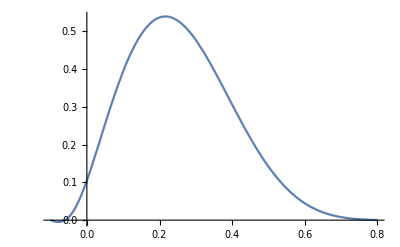

```mathematica
Plot[-I*(0.1)*sf1[x],{x,-0.1,0.8}]
```

```mathematica
1-2*0.01
```

0.98

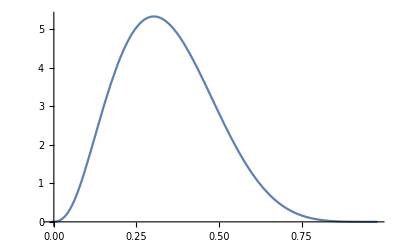

```mathematica
Plot[-I*sf1x1[x],{x,-0.01,0.98}]
```

```mathematica
sf1x1[0.98]
```

0.+1.99907×10^-7 ⅈ

```mathematica
sf2x1[0.98]
```

0.+1.99909×10^-7 ⅈ

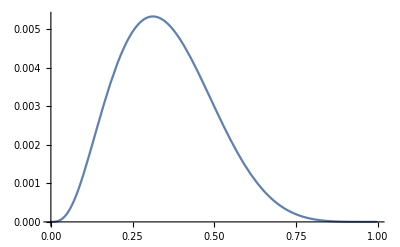

```mathematica
Plot[-I*(0.001)*sf1x2[x],{x,-0.001,0.998}]
```

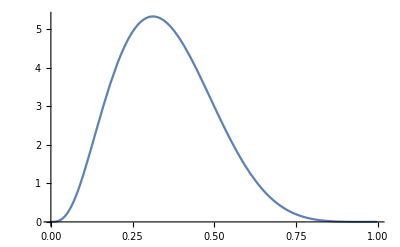

```mathematica
Plot[-I*sf1x2[x],{x,-0.001,0.998}]
```

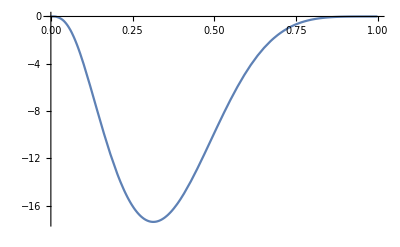

```mathematica
Plot[-I*sg1x2[x],{x,-0.001,0.998}]
```

```mathematica
sf1[0.5]
```

0.+1.41589 ⅈ

```mathematica
sf1x1[0.5]
```

0.+2.81677 ⅈ

```mathematica
inf12[y_]:=NIntegrate[nf12[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
inf22[y_]:=NIntegrate[nf22[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing12[y_]:=NIntegrate[ng12[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ing22[y_]:=NIntegrate[ng22[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
lf12=ParallelTable[{y,inf12[y]},{y,-0.2,0.6,0.02}];
lf22=ParallelTable[{y,inf22[y]},{y,0.6,1,0.02}];
lg12=ParallelTable[{y,ing12[y]},{y,-0.2,0.6,0.02}];
lg22=ParallelTable[{y,ing22[y]},{y,0.6,1,0.02}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 40 recursive bisections in θ near {k3,θ} = {0.146509412,1.538410912}. NIntegrate obtained -1.242448702×10^-7 ⅈ and 1.479831214×10^-10 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 40 recursive bisections in θ near {k3,θ} = {0.146509412,4.744774396}. NIntegrate obtained -5.976289436×10^-6 ⅈ and 1.826739427×10^-9 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

```mathematica
sf12=Interpolation[lf12];
sf22=Interpolation[lf22];
sg12=Interpolation[lg12];
sg22=Interpolation[lg22];
```

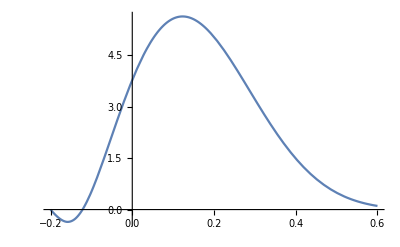

```mathematica
Plot[-I*sf12[x],{x,-0.2,0.6}]
```

```mathematica
sf12[0.6]
```

0.+0.106285 ⅈ

```mathematica
sf22[0.6]
```

0.+0.106285 ⅈ

```mathematica
sg12[0.6]
```

0.-0.620099 ⅈ

```mathematica
sg22[0.6]
```

0.-0.620099 ⅈ

```mathematica
path1x1=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-xix1.pdf"}];
Export[path1x1,Labeled[Show[Plot[(I)*(0.01)*sf1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.01)*sf2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-xix1.pdf

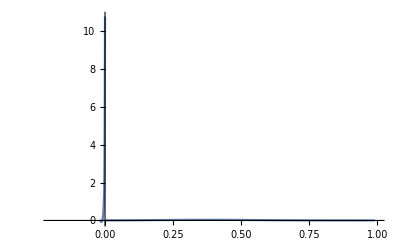

```mathematica
Show[Plot[(I)*(0.01)*sf1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All}],Plot[(I)*(0.01)*sf2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All}]]
```

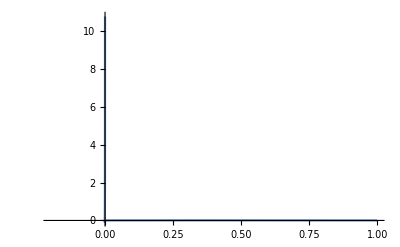

```mathematica
Show[Plot[(I)*(0.001)*sf1x2[x],{x,-0.002,0},PlotRange->{{-0.2,1},All}],Plot[(I)*(0.001)*sf2x2[x],{x,0,0.999},PlotRange->{{-0.2,1},All}]]
```

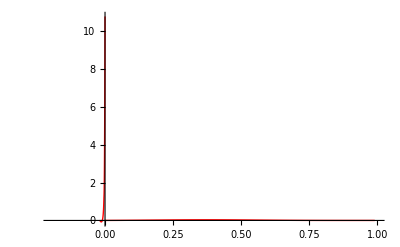

```mathematica
Show[Plot[(I)*(0.01)*sf1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.01)*sf2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]]
```

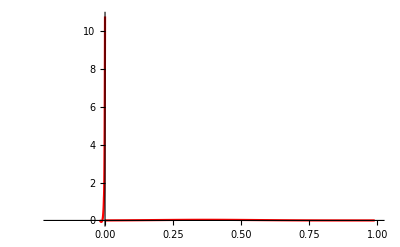
-Graphics-ξ f_fyξ=0.01

```mathematica
Labeled[Show[Plot[(I)*(0.01)*sf1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.01)*sf2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]
```

```mathematica
path1x2=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-xix2.pdf"}];
Export[path1x2,Labeled[Show[Plot[(I)*(0.001)*sf1x2[x],{x,-0.002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.001)*sf2x2[x],{x,0,0.999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-xix2.pdf

```mathematica
path1x3=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-f-xix3.pdf"}];
Export[path1x3,Labeled[Show[Plot[(I)*(0.0001)*sf1x3[x],{x,-0.0002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.0001)*sf2x3[x],{x,0,0.9999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[f,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.0001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-f-xix3.pdf

```mathematica
path1x3g=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-xix3.pdf"}];
Export[path1x3g,Labeled[Show[Plot[(I)*sg1x3[x],{x,-0.0002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*sg2x3[x],{x,0,0.9999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.0001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-xix3.pdf

```mathematica
path1x2g=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-xix2.pdf"}];
Export[path1x2g,Labeled[Show[Plot[(I)*sg1x2[x],{x,-0.002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*sg2x2[x],{x,0,0.999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.001"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-xix2.pdf

```mathematica
path1x1g=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"f-g-xix1.pdf"}];
Export[path1x1g,Labeled[Show[Plot[(I)*sg1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*sg2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\f-g-xix1.pdf

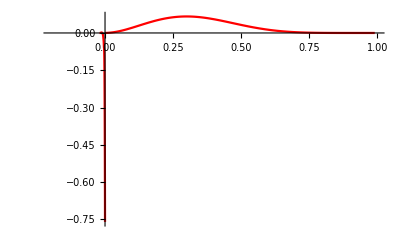
-Graphics-ξ g_fyξ=0.01

```mathematica
Labeled[Show[Plot[(I)*(0.01)*sg1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.01)*sg2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]
```

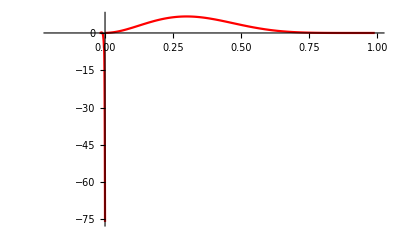
-Graphics-ξ g_fyξ=0.01

```mathematica
Labeled[Show[Plot[(I)*sg1x1[x],{x,-0.02,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*sg2x1[x],{x,0,0.99},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.01"},{Left,Bottom,Right},LabelStyle->24]
```

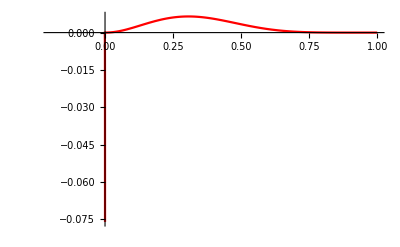
-Graphics-ξ g_fyξ=0.001

```mathematica
Labeled[Show[Plot[(I)*(0.001)*sg1x2[x],{x,-0.002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*(0.001)*sg2x2[x],{x,0,0.999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.001"},{Left,Bottom,Right},LabelStyle->24]
```

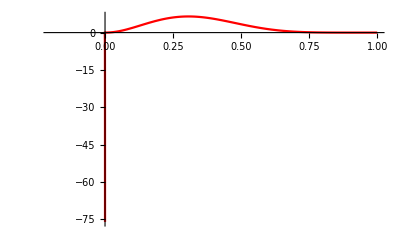
-Graphics-ξ g_fyξ=0.001

```mathematica
Labeled[Show[Plot[(I)*sg1x2[x],{x,-0.002,0},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],Plot[(I)*sg2x2[x],{x,0,0.999},PlotRange->{{-0.2,1},All},PlotStyle->{Red,Thick}],AxesStyle->Directive[16]],
{ξ*StyleBox[SubscriptBox[g,f],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.001"},{Left,Bottom,Right},LabelStyle->24]
```

```mathematica
sg2x2[0.3]
```

0.-6.4732 ⅈ

```mathematica
sg2x1[0.3]
```

0.-6.63694 ⅈ

```mathematica
sg2x3[0.3]
```

0.-6.45642 ⅈ

```mathematica
sg1x1[0]
```

0.+75.9808 ⅈ

```mathematica
sg1x2[0]
```

0.+75.9842 ⅈ

```mathematica
NIntegrate[y*nf1[y],{y,-0.2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[y*nf2[y],{y,0,0.9},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-0.568775251 ⅈ

```mathematica
NIntegrate[y*nf12[y],{y,-0.4,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[y*nf22[y],{y,0,0.8},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-0.615818866 ⅈ

```mathematica
NIntegrate[y*nf1[y-0.2],{y,0,0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[y*nf2[y-0.2],{y,0.2,1.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[0.2*nf3,{k3,0,∞},{θ,0,2π},{x,0,1}]
```

0.-0.764653 ⅈ

```mathematica
NIntegrate[y*nf1[y-0.2],{y,0,0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[y*nf2[y-0.2],{y,0.2,1.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.291672826 ⅈ